```mathematica
DDCCSet[n_]:= Module[
{result, binary, small, large},
binary = IntegerDigits[n,2];
large = FromDigits[binary,3];
small = FromDigits[binary /.{0->1,1->0},3];
result={large, large +small, large +2*small, 2*large, 2*large +small, 2*large +2*small}
]
```

```mathematica
Map[IntegerDigits[#,3]&,DDCCSet[FromDigits[{1,0,0},2]]]
```

{4,9,4}

{{1,0,0},{1,1,1},{1,2,2},{2,0,0},{2,1,1},{2,2,2}}

```mathematica
Table[DDCCSet[n],{n,1,100}]
```

{1,1,0}

{2,3,1}

{3,4,0}

{4,9,4}

{5,10,3}

{6,12,1}

{7,13,0}

{8,27,13}

{9,28,12}

{10,30,10}

{11,31,9}

{12,36,4}

{13,37,3}

{14,39,1}

{15,40,0}

{16,81,40}

{17,82,39}

{18,84,37}

{19,85,36}

{20,90,31}

{21,91,30}

{22,93,28}

{23,94,27}

{24,108,13}

{25,109,12}

{26,111,10}

{27,112,9}

{28,117,4}

{29,118,3}

{30,120,1}

{31,121,0}

{32,243,121}

{33,244,120}

{34,246,118}

{35,247,117}

{36,252,112}

{37,253,111}

{38,255,109}

{39,256,108}

{40,270,94}

{41,271,93}

{42,273,91}

{43,274,90}

{44,279,85}

{45,280,84}

{46,282,82}

{47,283,81}

{48,324,40}

{49,325,39}

{50,327,37}

{51,328,36}

{52,333,31}

{53,334,30}

{54,336,28}

{55,337,27}

{56,351,13}

{57,352,12}

{58,354,10}

{59,355,9}

{60,360,4}

{61,361,3}

{62,363,1}

{63,364,0}

{64,729,364}

{65,730,363}

{66,732,361}

{67,733,360}

{68,738,355}

{69,739,354}

{70,741,352}

{71,742,351}

{72,756,337}

{73,757,336}

{74,759,334}

{75,760,333}

{76,765,328}

{77,766,327}

{78,768,325}

{79,769,324}

{80,810,283}

{81,811,282}

{82,813,280}

{83,814,279}

{84,819,274}

{85,820,273}

{86,822,271}

{87,823,270}

{88,837,256}

{89,838,255}

{90,840,253}

{91,841,252}

{92,846,247}

{93,847,246}

{94,849,244}

{95,850,243}

{96,972,121}

{97,973,120}

{98,975,118}

{99,976,117}

{100,981,112}

{{1,1,1,2,2,2},{3,4,5,6,7,8},{4,4,4,8,8,8},{9,13,17,18,22,26},{10,13,16,20,23,26},{12,13,14,24,25,26},{13,13,13,26,26,26},{27,40,53,54,67,80},{28,40,52,56,68,80},{30,40,50,60,70,80},{31,40,49,62,71,80},{36,40,44,72,76,80},{37,40,43,74,77,80},{39,40,41,78,79,80},{40,40,40,80,80,80},{81,121,161,162,202,242},{82,121,160,164,203,242},{84,121,158,168,205,242},{85,121,157,170,206,242},{90,121,152,180,211,242},{91,121,151,182,212,242},{93,121,149,186,214,242},{94,121,148,188,215,242},{108,121,134,216,229,242},{109,121,133,218,230,242},{111,121,131,222,232,242},{112,121,130,224,233,242},{117,121,125,234,238,242},{118,121,124,236,239,242},{120,121,122,240,241,242},{121,121,121,242,242,242},{243,364,485,486,607,728},{244,364,484,488,608,728},{246,364,482,492,610,728},{247,364,481,494,611,728},{252,364,476,504,616,728},{253,364,475,506,617,728},{255,364,473,510,619,728},{256,364,472,512,620,728},{270,364,458,540,634,728},{271,364,457,542,635,728},{273,364,455,546,637,728},{274,364,454,548,638,728},{279,364,449,558,643,728},{280,364,448,560,644,728},{282,364,446,564,646,728},{283,364,445,566,647,728},{324,364,404,648,688,728},{325,364,403,650,689,728},{327,364,401,654,691,728},{328,364,400,656,692,728},{333,364,395,666,697,728},{334,364,394,668,698,728},{336,364,392,672,700,728},{337,364,391,674,701,728},{351,364,377,702,715,728},{352,364,376,704,716,728},{354,364,374,708,718,728},{355,364,373,710,719,728},{360,364,368,720,724,728},{361,364,367,722,725,728},{363,364,365,726,727,728},{364,364,364,728,728,728},{729,1093,1457,1458,1822,2186},{730,1093,1456,1460,1823,2186},{732,1093,1454,1464,1825,2186},{733,1093,1453,1466,1826,2186},{738,1093,1448,1476,1831,2186},{739,1093,1447,1478,1832,2186},{741,1093,1445,1482,1834,2186},{742,1093,1444,1484,1835,2186},{756,1093,1430,1512,1849,2186},{757,1093,1429,1514,1850,2186},{759,1093,1427,1518,1852,2186},{760,1093,1426,1520,1853,2186},{765,1093,1421,1530,1858,2186},{766,1093,1420,1532,1859,2186},{768,1093,1418,1536,1861,2186},{769,1093,1417,1538,1862,2186},{810,1093,1376,1620,1903,2186},{811,1093,1375,1622,1904,2186},{813,1093,1373,1626,1906,2186},{814,1093,1372,1628,1907,2186},{819,1093,1367,1638,1912,2186},{820,1093,1366,1640,1913,2186},{822,1093,1364,1644,1915,2186},{823,1093,1363,1646,1916,2186},{837,1093,1349,1674,1930,2186},{838,1093,1348,1676,1931,2186},{840,1093,1346,1680,1933,2186},{841,1093,1345,1682,1934,2186},{846,1093,1340,1692,1939,2186},{847,1093,1339,1694,1940,2186},{849,1093,1337,1698,1942,2186},{850,1093,1336,1700,1943,2186},{972,1093,1214,1944,2065,2186},{973,1093,1213,1946,2066,2186},{975,1093,1211,1950,2068,2186},{976,1093,1210,1952,2069,2186},{981,1093,1205,1962,2074,2186}}

```mathematica
DDCCSet[n_]:=With[{binary = IntegerDigits[n,2]},
With[{good=FromDigits[binary,3]},
DeleteDuplicates[
Select[
{
good,
FromDigits[binary /. {0->0,1->2},3],
FromDigits[binary /. {0->1,1->2},3],
FromDigits[binary /. {0->2,1->1},3],
FromDigits[binary /. {0->2,1->0},3]
}
,#≥good&
]
]
]
]
```

```mathematica
TableForm[
Table[
{FromDigits[IntegerDigits[n,2],3],Sort[Flatten[Table[DDCCSet[i],{i,1,n}]]]},
{n,1,27}
],
TableDepth->2
]
```

```mathematica
DDCCSet[n_]:=With[{binary = IntegerDigits[n,2]},
With[{good=FromDigits[binary,3]},
DeleteDuplicates[
Select[
{
good,
FromDigits[binary /. {0->0,1->2},3],
FromDigits[binary /. {0->1,1->2},3],
FromDigits[binary /. {0->2,1->1},3],
FromDigits[binary /. {0->2,1->0},3]
}
,#≥good&
]
]
]
]
```

```mathematica
MakeReplace[list_]:=Table[i-1->list[[i]],{i,1,Length[list]}]
```

```mathematica
ReplacesFor[p_]:=Map[Last,Select[Table[{Select[t,#>=Quotient[p+1,2]&],t}, {t,Tuples[Range[0,p-1],{p-1}]}],#[[1]]≠{}&]]
```

```mathematica
DDCCSet[n_,p_]:=Module[
{half = Quotient[p+1,2],
replaces=Map[MakeReplace[#]&, ReplacesFor[p]],
binary,
good
},
binary = IntegerDigits[n,half];
good=FromDigits[binary,p];
DeleteDuplicates[
Sort[
Select[
Table[FromDigits[binary /. r,p],{r,replaces}]
,#≥good&
]
]
]
]
```

```mathematica
DDCCSet[n_,p_, half_,replaces_]:=Module[
{binary,
good
},
binary = IntegerDigits[n,half];
good=FromDigits[binary,p];
DeleteDuplicates[
Sort[
Select[
Table[FromDigits[binary /. r,p],{r,replaces}]
,#≥good&
]
]
]
]
```

```mathematica
IndexOfGoodForPrime[n_,p_] := FromDigits[IntegerDigits[n,p],(p+1)/2]
```

```mathematica
DDCCCalc[p_,pow_]:= Module[
{half = Quotient[p+1,2],
replaces=Map[MakeReplace[#]&, ReplacesFor[p]],
current,
result={},
count
},
count = IndexOfGoodForPrime[p^pow,p];
Monitor[
For[current=1,current < count, current++,
result=Join[result,DDCCSet[current,p,half,replaces]]
],
{pow,current,count,Length[result]}
];
Return[DeleteDuplicates[Sort[result]]]
]
```

```mathematica
Table[Length[DDCCCalc[7,i]],{i,1,5}]
```

{6,48,342,2400,14646}

```mathematica
DDCCCalc[5,3]
```

{{2,3,4},{12,18,24},{62,93,124},{1,2,3,4},{6,12,18,24},{31,62,93,124},{11,12,13,14,15,16,17,18,19,20,21,22,23,24},{56,62,68,74,75,81,87,93,99,100,106,112,118,124},{57,62,67,72,78,83,88,93,98,104,109,114,119,124},{61,62,63,64,90,91,92,93,94,120,121,122,123,124},{10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{50,56,62,68,74,75,81,87,93,99,100,106,112,118,124},{52,57,62,67,72,78,83,88,93,98,104,109,114,119,124},{60,61,62,63,64,90,91,92,93,94,120,121,122,123,124},{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{32,33,34,60,61,62,63,64,90,91,92,93,94,120,121,122,123,124},{36,41,46,52,57,62,67,72,78,83,88,93,98,104,109,114,119,124},{37,43,49,50,56,62,68,74,75,81,87,93,99,100,106,112,118,124},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{25,31,37,43,49,50,56,62,68,74,75,81,87,93,99,100,106,112,118,124},{26,31,36,41,46,52,57,62,67,72,78,83,88,93,98,104,109,114,119,124},{30,31,32,33,34,60,61,62,63,64,90,91,92,93,94,120,121,122,123,124},{55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124},{51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124},{35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124},{27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124}}

```mathematica
Table[Length[DDCCSet[i,3]],{i,1,10}]
```

{2,4,2,4,4,4,2,4,4,4}

```mathematica
With[
{p=3},
Table[{Select[t,#>=Quotient[p+1,2]&],t}, {t,Tuples[Range[0,p-1],{p}]}]
]
```

{{{},{0,0,0}},{{},{0,0,1}},{{2},{0,0,2}},{{},{0,1,0}},{{},{0,1,1}},{{2},{0,1,2}},{{2},{0,2,0}},{{2},{0,2,1}},{{2,2},{0,2,2}},{{},{1,0,0}},{{},{1,0,1}},{{2},{1,0,2}},{{},{1,1,0}},{{},{1,1,1}},{{2},{1,1,2}},{{2},{1,2,0}},{{2},{1,2,1}},{{2,2},{1,2,2}},{{2},{2,0,0}},{{2},{2,0,1}},{{2,2},{2,0,2}},{{2},{2,1,0}},{{2},{2,1,1}},{{2,2},{2,1,2}},{{2,2},{2,2,0}},{{2,2},{2,2,1}},{{2,2,2},{2,2,2}}}

```mathematica
DDCCSet[3]
```

{4,8}

```mathematica
FromDigits[IntegerDigits[38,2],3]
```

255

```mathematica
IntegerDigits[38,3]
```

{1,1,0,2}

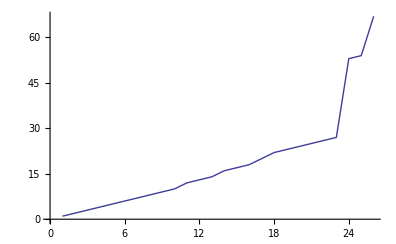

```mathematica
ListLinePlot[Sort[Flatten[Table[DDCCSet[i],{i,1,8}]]]]
```